# Bounds from Selberg trace formula

## Selberg Trace Formula functions

```mathematica
Clear[scalarEllipticSum, scalarEllipticSumEv, 
   spinorEllipticSum, spinorEllipticSumEv, 
   scalarHyperbolicSum, spinorHyperbolicSum, 
   scalarVolumeTerm, scalarVolumeTermEv, spinorVolumeTerm, 
   spinorVolumeTermEv, xScalar, xSpinor, a, b, cVectorNew, 
   precision, hBasicNew, gSelberg, ghatSelberg, 
   probingEigenScalar, probingEigenSpinor, scalarAMatrix, 
   spinorAMatrix]; 
precision = 12; 
hBasicNew[x_, δ_] := 
   Piecewise[{{(4*δ^3)/3, x < 0 && 2*δ + x == 0}, 
      {(16*δ^3)/3 - x^3/2 - 2*δ*x^2, x == 0 || 
        (x < 0 && 2*δ + x > 0)}, {(16*δ^3)/3 + x^3/2 - 
        2*δ*x^2, x > 0 && x < 2*δ}, {(-(1/6))*(x - 4*δ)^3, 
       x > 0 && (x == 2*δ || (x < 4*δ && 2*δ <= x))}, 
      {(1/6)*(4*δ + x)^3, 2*δ + x < 0 && 4*δ + x > 0}}, 0]/
    (16*δ^4); 
hprimeBasicNew[k_, x_, δ_] := 
   (1/2)*(hBasicNew[δ*k + x, δ] + hBasicNew[x - δ*k, δ]); 
fProbeNew[x_, δ_] := (1/(256*δ^8))*
    Piecewise[{{-((x - 8*δ)^7/5040), x > 0 && δ > 0 && 
        x < 8*δ && 6*δ <= x}, {(x + 8*δ)^7/5040, 
       x < 0 && δ > 0 && x + 6*δ <= 0 && x + 8*δ > 0}, 
      {-(((x + 6*δ)^4*(3*x^3 + 40*δ*x^2 + 72*δ^2*x - 
           640*δ^3))/2520), x < 0 && δ > 0 && 
        x + 4*δ == 0}, {((x - 6*δ)^4*(3*x^3 - 40*δ*x^2 + 
          72*δ^2*x + 640*δ^3))/2520, x > 0 && δ > 0 && 
        x == 4*δ}, {-(x^7/720) - (δ*x^6)/18 - 
        (14*δ^2*x^5)/15 - (76*δ^3*x^4)/9 - 
        (392*δ^4*x^3)/9 - (368*δ^5*x^2)/3 - 
        (6944*δ^6*x)/45 - (8896*δ^7)/315, 
       x < 0 && δ > 0 && x + 4*δ < 0 && x + 6*δ > 0}, 
      {x^7/720 - (δ*x^6)/18 + (14*δ^2*x^5)/15 - 
        (76*δ^3*x^4)/9 + (392*δ^4*x^3)/9 - 
        (368*δ^5*x^2)/3 + (6944*δ^6*x)/45 - 
        (8896*δ^7)/315, x > 0 && δ > 0 && x < 6*δ && 
        4*δ < x}, {(1/315)*(-x^7 + 84*δ^2*x^5 - 
         2240*δ^4*x^3 - 3360*δ^5*x^2 + 8960*δ^6*x + 
         19328*δ^7), x == 0 && δ > 0}, 
      {-(x^7/144) - (δ*x^6)/18 + (8*δ^3*x^4)/9 - 
        (32*δ^5*x^2)/3 + (19328*δ^7)/315, 
       x < 0 && δ > 0 && x + 2*δ > 0}, 
      {x^7/144 - (δ*x^6)/18 + (8*δ^3*x^4)/9 - 
        (32*δ^5*x^2)/3 + (19328*δ^7)/315, 
       x < 2*δ && x > 0 && δ > 0}, 
      {-(x^7/240) + (δ*x^6)/10 - (14*δ^2*x^5)/15 + 
        4*δ^3*x^4 - (56*δ^4*x^3)/9 - (16*δ^5*x^2)/5 - 
        (224*δ^6*x)/45 + (6592*δ^7)/105, 
       x < 4*δ && 2*δ < x && x > 0 && δ > 0}, 
      {x^7/240 + (δ*x^6)/10 + (14*δ^2*x^5)/15 + 
        4*δ^3*x^4 + (56*δ^4*x^3)/9 - (16*δ^5*x^2)/5 + 
        (224*δ^6*x)/45 + (6592*δ^7)/105, 
       x < 0 && x + 2*δ < 0 && δ > 0 && x + 4*δ > 0}, 
      {-(x^7/336) + (δ*x^6)/18 - (4*δ^2*x^5)/15 - 
        (8*δ^3*x^4)/9 + (98*δ^4*x^3)/9 - (64*δ^5*x^2)/3 - 
        (368*δ^6*x)/9 + (4544*δ^7)/35, x == 2*δ && 
        x > 0 && δ > 0}, {x^7/336 + (δ*x^6)/18 + 
        (4*δ^2*x^5)/15 - (8*δ^3*x^4)/9 - (98*δ^4*x^3)/9 - 
        (64*δ^5*x^2)/3 + (368*δ^6*x)/9 + (4544*δ^7)/35, 
       x + 2*δ == 0 && x < 0 && δ > 0}}, 0]; 
gSelberg[a_, b_, x_, δ_] := 
   (1/4)*(fProbeNew[δ*(a - b) + x, δ] + 
     fProbeNew[δ*(b - a) + x, δ] + 
     fProbeNew[δ*(a + b) + x, δ] + 
     fProbeNew[x - δ*(a + b), δ]); 
ghatSelberg[a_, b_, x_, δ_] := (Sin[δ*x]/(δ*x))^8*
    Cos[a*δ*x]*Cos[b*δ*x];
```

```mathematica
(*For the scalar STF*)
```

```mathematica
scalarEllipticSum[kInverse_][h_]:=Module[{},Return[Total[Table[Total[Table[kInverse[[i]]/(4*Sin[v*Pi*kInverse[[i]]])*NIntegrate[h*Cosh[Pi*(1-2 v*kInverse[[i]])*x]/Cosh[Pi*x],{x,-Infinity,Infinity},PrecisionGoal->12,WorkingPrecision->20,Method->"GaussKronrodRule",MaxRecursion->20],{v,1,1/kInverse[[i]]-1}]],{i,1,Length[kInverse]}]]]];
scalarVolumeTerm[g_,kInverse_][h_]:=((g-1)+If[Total[kInverse]>0,1/2*(Length[kInverse]-Total[kInverse]),0])*NIntegrate[x*Tanh[Pi*x]*h,{x,-Infinity,Infinity},PrecisionGoal->12,WorkingPrecision->500,MaxRecursion->100,Method->"ExtrapolatingOscillatory"]//SetPrecision[#,precision]&;
scalarHyperbolicSum[geodesicList_][h_]:=SetPrecision[Total[(#[[2]]*Abs[#[[1]]]/(2 Sinh[Abs[#[[1]]]/2])*h[Abs[#[[1]]]])&/@geodesicList],precision];
```

```mathematica
(* For the spinor STF*)
```

```mathematica
spinorEllipticSum[kInverse_][h_]:=Module[{},Return[Total[Table[Total[Table[(ⅈ*kInverse[[i]]*Sign[1/2-v*kInverse[[i]]])/(4Sin[v*Pi*kInverse[[i]]])*NIntegrate[h*(Exp[x]-Exp[2 ⅈ v*kInverse[[i]]*Pi])/(Cosh[x]-Cos[Pi*(1-2 v*kInverse[[i]])]),{x,-Infinity,Infinity},PrecisionGoal->12,WorkingPrecision->20,Method->"GaussKronrodRule",MaxRecursion->20],{v,1,1/kInverse[[i]]-1}]],{i,1,Length[kInverse]}]]]];
spinorVolumeTerm[g_,kInverse_][h_]:=((g-1)+If[Total[kInverse]>0,1/2*(Length[kInverse]-Total[kInverse]),0])*NIntegrate[x*Coth[Pi*x]*h,{x,-Infinity,Infinity},PrecisionGoal->12,WorkingPrecision->500,MaxRecursion->100,Method->"ExtrapolatingOscillatory"]//SetPrecision[#,precision]&;
spinorHyperbolicSum[geodesicList_][h_]:=SetPrecision[Total[((#[[4]])/(#[[2]])*Abs[#[[1]]]/(2 Sinh[Abs[#[[1]]]/2])*h[Abs[#[[1]]]])&/@geodesicList],precision];
```

```mathematica
scalarVolumeTermEv[g_,kInverse_][range_,n_]:=(scalarVolumeTermEv[g,kInverse][range,n]=Module[{δ,result},δ=range/(2*n+8);result=Table[SetPrecision[scalarVolumeTerm[g,kInverse][ghatSelberg[a,b,x,δ]],precision],{a,0,n},{b,0,n}];Return[result]]);
scalarEllipticSumEv[g_,kInverse_][range_:7,n_:25]:=(scalarEllipticSumEv[g,kInverse][range,n]=Module[{δ,result},δ=range/(2*n+8);result=Table[SetPrecision[(If[Total[kInverse]>0,(scalarEllipticSum[kInverse][ghatSelberg[a,b,x,δ]]),0]),precision],{a,0,n},{b,0,n}];Return[result]]);
spinorVolumeTermEv[g_,kInverse_][range_,n_]:=(spinorVolumeTermEv[g,kInverse][range,n]=Module[{δ,result},δ=range/(2*n+8);result=Table[SetPrecision[spinorVolumeTerm[g,kInverse][ghatSelberg[a,b,x,δ]],precision],{a,0,n},{b,0,n}];Return[result]]);
spinorEllipticSumEv[g_,kInverse_][range_:7,n_:25]:=(spinorEllipticSumEv[g,kInverse][range,n]=Module[{δ,result},δ=range/(2*n+8);result=Table[(If[Total[kInverse]>0,(spinorEllipticSum[kInverse][ghatSelberg[a,b,x,δ]]),0]),{a,0,n},{b,0,n}];Return[result]]);scalarAMatrix[g_,kInverse_,geodesicList_][range_:7,n_:25]:=(scalarAMatrix[g,kInverse,geodesicList][range,n]=Module[{δ,result},δ=range/(2*n+8);result=Table[SetPrecision[scalarVolumeTermEv[g,kInverse][range,n][[a+1,b+1]]+scalarHyperbolicSum[geodesicList][gSelberg[a,b,#,δ]&] +(If[Total[kInverse]>0,(scalarEllipticSumEv[g,kInverse][range,n][[a+1,b+1]]),0]),precision],{a,0,n},{b,0,n}];Return[result]]);
spinorAMatrix[g_,kInverse_,geodesicList_][range_:7,n_:25]:=(spinorAMatrix[g,kInverse,geodesicList][range,n]=Module[{δ,result},δ=range/(2*n+8);result=Table[SetPrecision[spinorVolumeTermEv[g,kInverse][range,n][[a+1,b+1]]+spinorHyperbolicSum[geodesicList][gSelberg[a,b,#,δ]&] +(If[Total[kInverse]>0,(Chop[spinorEllipticSumEv[g,kInverse][range,n][[a+1,b+1]],10^-precision]),0]),precision],{a,0,n},{b,0,n}];Return[result]]);
```

```mathematica
cVectorNew[range_,n_]:=(cVectorNew[range,n]=Module[{δ},δ=range/(2*n+8);Return[Table[SetPrecision[(Sin[δ t]/(δ t))^4*Cos[k δ t],precision],{k,0,n}]]]);
checkingPositivityOfEigenvalues[matrix_]:=Min[Eigenvalues[matrix]]>0; 
xScalar[aMatrix_][range_,n_]:=(xScalar[aMatrix][range,n]=LinearSolve[aMatrix,cVectorNew[range,n]]);
probingEigenScalar[aMatrix_][range_,n_][λ_]:=SetPrecision[1/(xScalar[aMatrix][range,n].cVectorNew[range,n])/.t->-Sqrt[λ-1/4],12];
xSpinor[aMatrix_][range_,n_]:=(xSpinor[aMatrix][range,n]=LinearSolve[aMatrix,cVectorNew[range,n]]);
probingEigenSpinor[aMatrix_][range_,n_][λ_]:=SetPrecision[1/(xSpinor[aMatrix][range,n].cVectorNew[range,n])/.t->-Sqrt[λ-1/4],12];
```

```mathematica
xFunc[aMatrix_][range_,n_]:=LinearSolve[aMatrix,cVectorNew[range,n]];
probingEigenValue[aMatrix_][range_,n_][λ_]:=SetPrecision[1/(xFunc[aMatrix][range,n].cVectorNew[range,n])/.t->-Sqrt[λ-1/4],12];
```

### peak-finding function

```mathematica
(*JAMES NOTEBOOK*)
binarySearchforPeak[function_,true0_,false0_,precision_, doubleLimit_:8] := 
 Module[{true, false,output,counter},
  false = false0;
  true = true0;
(*Double the starting false point up to doubleLimit times until it returns false*)
counter=0;
While[TrueQ[function[false]],counter=counter+1;If[counter<doubleLimit,Print["Doubled starting False: "~~ToString[counter]];
true=false;
false=2false,Break[]]];
(*Halve the starting true point up to doubleLimit times until it returns true*)
If[counter<doubleLimit,
counter=0;
While[Not[TrueQ[function[true]]],counter=counter+1;If[counter<doubleLimit,Print["Halved starting True: "~~ToString[counter]];
false=true;
true=1/2true,Break[]]];
];
output=If[counter<doubleLimit, While[Abs[true - false] > precision,
   If[function[(true + false)/2], 
true = (true + false)/2;, 
false = (true + false)/2;
];
   ]; false,
Print["Could not find a False point so returning infinity"];Infinity];
lastFalse=false;
lastTrue=true;
output
  ];
nMin[func_,tMin_,tMax_,precision_]:=Module[{counter,leftPt,rightPt,midPt,newPt},
counter=0;
leftPt=tMin;
rightPt=tMax;
midPt=(leftPt+rightPt)/2;
While[counter<5000&&Abs[leftPt-rightPt]>precision/2,
counter=counter+1;
If[Abs[leftPt-midPt]>Abs[rightPt-midPt],
newPt=(leftPt+midPt)/2;If[func[newPt]>func[midPt],leftPt=newPt, rightPt=midPt; midPt=newPt];,
newPt=(rightPt+midPt)/2;If[func[newPt]>func[midPt],rightPt=newPt, leftPt=midPt; midPt=newPt];
];
];
If[counter==5000,Print["maxed out counter"]];
midPt
]
(*find the location and height of a peak in a given interval, and an interval containing the true peak*)
(*Clear[findPeakScalar]
findPeakScalar[g_,kInverse_,geodesicList_,range_,n_,{tMin_,tMax_}, prec_:10^(-13), conservativeOutput_:False]:=Module[{peak,height,heightRound,lowerBound,upperBound,lowerBoundConservative,upperBoundConservative,xTest,diff},
Print[{tMin,tMax}];
peak=nMin[-probingEigenScalar[g,kInverse,geodesicList][range,n][#]&,tMin,tMax,prec];
height=probingEigenScalar[g,kInverse,geodesicList][range,n][peak];
heightRound=Floor[height];
lowerBound=binarySearchforPeak[((probingEigenScalar[g,kInverse,geodesicList][range,n][#]-heightRound)<=0)&,tMin,peak,prec,5];
If[tMin<1/100&&lowerBound==Infinity,lowerBound=0];
upperBound=binarySearchforPeak[((probingEigenScalar[g,kInverse,geodesicList][range,n][#]-heightRound)>=0)&,peak,tMax,prec,5];
If[Not[heightRound==1],
lowerBoundConservative=binarySearchforPeak[((probingEigenScalar[g,kInverse,geodesicList][range,n][#]-1)<=0)&,tMin,peak,prec,5];
upperBoundConservative=binarySearchforPeak[((probingEigenScalar[g,kInverse,geodesicList][range,n][#]-1)>=0)&,peak,tMax,prec,5];,
lowerBoundConservative=lowerBound;
upperBoundConservative=upperBound;
];
If[Not[heightRound==1],
Print[" The local peak is at "~~ToString[N[peak,-Log[10,prec]]]~~" with height "~~ToString[N[height,-Log[10,prec]]]~~". The bound exceeds "~~ToString[ heightRound]~~" in the interval "~~ToString[N[{lowerBound,upperBound},-Log[10,prec]]]~~" and exceeds 1 in the interval "~~ToString[N[{lowerBoundConservative,upperBoundConservative},-Log[10,prec]]]~~"."];,
Print["The local peak is at "~~ToString[N[peak,-Log[10,prec]]]~~" with height "~~ToString[N[height,-Log[10,prec]]]~~". The bound exceeds 1 in the interval "~~ToString[N[{lowerBound,upperBound},-Log[10,prec]]]~~"."];
];
If[conservativeOutput,{lowerBoundConservative,upperBoundConservative}]
];*)


peakScalar[aMatrix_,range_,n_,{tMin_,tMax_}, prec_:10^(-13), conservativeOutput_:False]:=Module[{peak,height,heightRound,lowerBound,upperBound,lowerBoundConservative,upperBoundConservative,xTest,diff},
Print[{tMin,tMax}];
peak=nMin[-probingEigenValue[aMatrix][range,n][#]&,tMin,tMax,prec];
height=probingEigenValue[aMatrix][range,n][peak];
heightRound=Floor[height];
lowerBound=binarySearchforPeak[((probingEigenValue[aMatrix][range,n][#]-heightRound)<=0)&,tMin,peak,prec,5];
If[tMin<1/100&&lowerBound==Infinity,lowerBound=0];
upperBound=binarySearchforPeak[((probingEigenValue[aMatrix][range,n][#]-heightRound)>=0)&,peak,tMax,prec,5];
If[Not[heightRound==1],
lowerBoundConservative=binarySearchforPeak[((probingEigenValue[aMatrix][range,n][#]-1)<=0)&,tMin,peak,prec,5];
upperBoundConservative=binarySearchforPeak[((probingEigenValue[aMatrix][range,n][#]-1)>=0)&,peak,tMax,prec,5];,
lowerBoundConservative=lowerBound;
upperBoundConservative=upperBound;
];
If[Not[heightRound==1],
Print[" The local peak is at "~~ToString[N[peak,-Log[10,prec]]]~~" with height "~~ToString[N[height,-Log[10,prec]]]~~". The bound exceeds "~~ToString[ heightRound]~~" in the interval "~~ToString[N[{lowerBound,upperBound},-Log[10,prec]]]~~" and exceeds 1 in the interval "~~ToString[N[{lowerBoundConservative,upperBoundConservative},-Log[10,prec]]]~~"."];,
Print["The local peak is at "~~ToString[N[peak,-Log[10,prec]]]~~" with height "~~ToString[N[height,-Log[10,prec]]]~~". The bound exceeds 1 in the interval "~~ToString[N[{lowerBound,upperBound},-Log[10,prec]]]~~"."];
];
If[conservativeOutput,{lowerBoundConservative,upperBoundConservative}]
];



(*Clear[findPeakSpinor]
findPeakSpinor[g_,kInverse_,geodesicList_,range_,n_,{tMin_,tMax_}, prec_:10^(-13), conservativeOutput_:False]:=Module[{peak,height,heightRound,lowerBound,upperBound,lowerBoundConservative,upperBoundConservative,xTest,diff},
Print[{tMin,tMax}];
peak=nMin[-probingEigenSpinor[g,kInverse,geodesicList][range,n][#]&,tMin,tMax,prec];
height=probingEigenSpinor[g,kInverse,geodesicList][range,n][peak];
heightRound=Floor[height];
lowerBound=binarySearchforPeak[((probingEigenSpinor[g,kInverse,geodesicList][range,n][#]-heightRound)<=0)&,tMin,peak,prec,6];
If[tMin<1/100&&lowerBound==Infinity,lowerBound=0];
upperBound=binarySearchforPeak[((probingEigenSpinor[g,kInverse,geodesicList][range,n][#]-heightRound)>=0)&,peak,tMax,prec,6];
If[Not[heightRound==2],
lowerBoundConservative=binarySearchforPeak[((probingEigenSpinor[g,kInverse,geodesicList][range,n][#]-2)<=0)&,tMin,peak,prec,6];
upperBoundConservative=binarySearchforPeak[((probingEigenSpinor[g,kInverse,geodesicList][range,n][#]-2)>=0)&,peak,tMax,prec,6];,
lowerBoundConservative=lowerBound;
upperBoundConservative=upperBound;
];
If[Not[heightRound==2],
Print[" The local peak is at "~~ToString[N[peak,-Log[10,prec]]]~~" with height "~~ToString[N[height,-Log[10,prec]]]~~". The bound exceeds "~~ToString[ heightRound]~~" in the interval "~~ToString[N[{lowerBound,upperBound},-Log[10,prec]]]~~" and exceeds 2 in the interval "~~ToString[N[{lowerBoundConservative,upperBoundConservative},-Log[10,prec]]]~~"."];,
Print["The local peak is at "~~ToString[N[peak,-Log[10,prec]]]~~" with height "~~ToString[N[height,-Log[10,prec]]]~~". The bound exceeds 2 in the interval "~~ToString[N[{lowerBound,upperBound},-Log[10,prec]]]~~"."];
];
If[conservativeOutput,{lowerBoundConservative,upperBoundConservative}]
]*)

peakSpinor[aMatrix_,range_,n_,{tMin_,tMax_}, prec_:10^(-13), conservativeOutput_:False]:=Module[{peak,height,heightRound,lowerBound,upperBound,lowerBoundConservative,upperBoundConservative,xTest,diff},
Print[{tMin,tMax}];
peak=nMin[-probingEigenValue[aMatrix][range,n][#]&,tMin,tMax,prec];
height=probingEigenValue[aMatrix][range,n][peak];
heightRound=Floor[height];
lowerBound=binarySearchforPeak[((probingEigenValue[aMatrix][range,n][#]-heightRound)<=0)&,tMin,peak,prec,6];
If[tMin<1/100&&lowerBound==Infinity,lowerBound=0];
upperBound=binarySearchforPeak[((probingEigenValue[aMatrix][range,n][#]-heightRound)>=0)&,peak,tMax,prec,6];
If[Not[heightRound==2],
lowerBoundConservative=binarySearchforPeak[((probingEigenValue[aMatrix][range,n][#]-2)<=0)&,tMin,peak,prec,6];
upperBoundConservative=binarySearchforPeak[((probingEigenValue[aMatrix][range,n][#]-2)>=0)&,peak,tMax,prec,6];,
lowerBoundConservative=lowerBound;
upperBoundConservative=upperBound;
];
If[Not[heightRound==2],
Print[" The local peak is at "~~ToString[N[peak,-Log[10,prec]]]~~" with height "~~ToString[N[height,-Log[10,prec]]]~~". The bound exceeds "~~ToString[ heightRound]~~" in the interval "~~ToString[N[{lowerBound,upperBound},-Log[10,prec]]]~~" and exceeds 2 in the interval "~~ToString[N[{lowerBoundConservative,upperBoundConservative},-Log[10,prec]]]~~"."];,
Print["The local peak is at "~~ToString[N[peak,-Log[10,prec]]]~~" with height "~~ToString[N[height,-Log[10,prec]]]~~". The bound exceeds 2 in the interval "~~ToString[N[{lowerBound,upperBound},-Log[10,prec]]]~~"."];
];
If[conservativeOutput,{lowerBoundConservative,upperBoundConservative}]
];
```

## example

```mathematica
(*The input from the . mx file is of the form {... {length, winding number, multiplicity, multiplicity with sign} ...} . For non - spin orbifold, the last entry should be ignored. *)
```

```mathematica
geodesics237={#[[1]],(#[[3]])/(#[[2]])}&/@Import[NotebookDirectory[]~~"/geodesics/geodesics-237_cutoff-4pt5_precision_10_epsilon-0pt1.mx"];
```

```mathematica
(*Once we have a geodesic list of the form {...{length, multiplicity/winding}...},throw it into scalarAMatrix (scalarAMatrix[genus,{1/k1,1/k2,1/k3},geodesicList][cutoff,dimension_of_the_amatrix]) to evaluate the A matrix in Lin-Lipnowski algorithm.

As a sanity check, make sure amatrix only has positive eigenvalues
  After getting the amatrix,use peakScalar[amatrix,cutoff,dimension_of_amatrix,{lowerbound,upperbound}] to get the location of the peak within the interval {lowerbound,upperbound}
To get a reasonablly sharp peak, try dimension_of_the_amatrix=19. Increasing the dimension tends to trade the sharpness of later peaks for the sharpness of the first few peaks.
*)
```

```mathematica
Monitor[amatrix=scalarAMatrix[0,{1/2,1/3,1/7},geodesics237][45/10,3];,{a,b}]
```

$Aborted

```mathematica
amatrix//Eigenvalues//Sort
```

{2.39747753739×10^-7,2.90544965136×10^-6,0.00116550571194,4.53765005679}

```mathematica
curve=probingEigenValue[amatrix][45/10,3][λ];
```

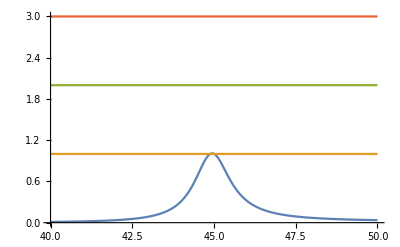

```mathematica
Plot[{curve,1,2,3},{λ,40
,50},PlotRange->{All,All},MaxRecursion->15]
```

```mathematica
peakScalar[amatrix,45/10,3,{44,46}]
```

{44,46}

The local peak is at 44.94475555420 with height 1.00760540447. The bound exceeds 1 in the interval {44.88631726514, 45.00362292488}.

```mathematica
bolzaMPPPGeolist=Import["/Users/yixinxu/Nutstore Files/Nutstore/Physics/Ongoing Research/Automorphic Bootstrap/HyperFun/geodesics/Bolza-MPPP-geodesic.xml"];
```

```mathematica
bolzaPMPMGeolist=Import["/Users/yixinxu/Nutstore Files/Nutstore/Physics/Ongoing Research/Automorphic Bootstrap/HyperFun/geodesics/Bolza-PMPM-geodesic.xml"];
```

```mathematica
bolzaPPMMGeolist=Import["/Users/yixinxu/Nutstore Files/Nutstore/Physics/Ongoing Research/Automorphic Bootstrap/HyperFun/geodesics/Bolza-PPMM-geodesic.xml"];
```

```mathematica
Monitor[amatrixPPMM=scalarAMatrix[2,{1/1,1/1,1/1},bolzaPPMMGeolist][1064/100,24];,{a,b}]
```

$Aborted

```mathematica
amatrixMPPP//Eigenvalues
```

{158.53439293,61.1402396759,45.4835141766,32.2646759216,22.9376362503,19.7031125461,16.9011651597,8.66351771209,7.03908719319,5.92988357955,3.93964432077,3.7201464997,1.56578253521,1.03712294835,0.615203661566,0.258270544613,0.0867025254591,0.0309389031646,0.00857634269319,0.00217656149627,0.000372013653828,0.000219414963651,0.0000341360165109,1.67732654362×10^-6,1.24287140015×10^-8}

```mathematica
curve=probingEigenValue[amatrixMPPP][1064/100,24][λ];
```

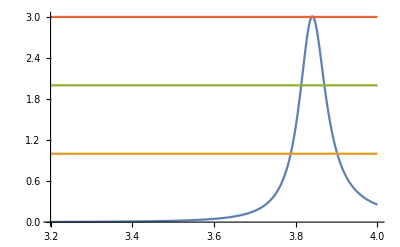

```mathematica
Plot[{curve,1,2,3},{λ,3.2
,4},PlotRange->{All,All},MaxRecursion->15]
```

```mathematica
peakScalar[amatrixMPPP,1064/100,24,{3,4}]
```

{3,4}

The local peak is at 3.840825557709 with height 3.00712328939. The bound exceeds 3 in the interval {3.838886940769, 3.842772834639} and exceeds 1 in the interval {3.787730700529, 3.901587555325}.

```mathematica
Monitor[spinoramatrixPPMM=spinorAMatrix[2,{1/1,1/1,1/1},bolzaPPMMGeolist][1064/100,24];,{a,b}]
```

```mathematica
Monitor[spinoramatrixPMPM=spinorAMatrix[2,{1/1,1/1,1/1},bolzaPMPMGeolist][1064/100,24];,{a,b}]
```

```mathematica
curve=probingEigenValue[spinoramatrixPPMM][1064/100,24][λ];
```

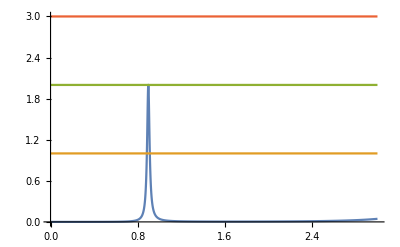

```mathematica
Plot[{curve,1,2,3},{λ,0
,3},PlotRange->{All,All},MaxRecursion->15]
```

```mathematica
peakSpinor[spinoramatrixPPMM,1064/100,24,{5/10,12/10}]
```

{1/2,6/5}

The local peak is at 0.8972760319710 with height 2.00074549172. The bound exceeds 2 in the interval {0.8970133121437, 0.8975387540243}.

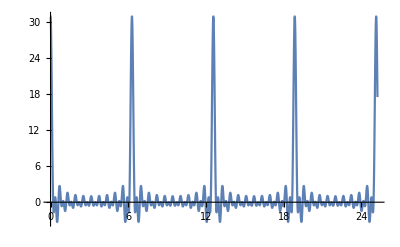

```mathematica
Plot[{Sum[Cos[n x],{n,-10,20}]},{x,0,8 Pi+0.1},PlotRange->All,MaxRecursion->10]
```